```mathematica
(*generation of the distribution to be used in the calculation of the field components*)
n=100;
λ=1;
k=2*Pi/λ; 
alpha=0.75;
alphamax=1.25;
min=-2;max=2;
zmin=-2;zmax=2;
step=100;
f=1;l0=1;
A = Pi*f*l0/λ;β=3/2;
urad[z_]:=k*(z*λ)*(Sin[alphamax]^2);
uazi[z_]:=k*(z*λ)*(Sin[alpha]^2);
v2drad = Table[{k*Sin[alphamax]*√(i^2+j^2),z},{i,Range[min λ,max λ,(max-min)/step λ]},{j,Range[min λ,max λ,(max-min)/step λ]},{z,Range[zmin,zmax,1]}];
v2dazi=Table[{k*Sin[alpha]*√(i^2+j^2),z},{i,Range[min λ,max λ,(max-min)/step λ]},{j,Range[min λ,max λ,(max-min)/step λ]},{z,Range[zmin,zmax,1]}];
v1drad= Abs[Table[{k*Sin[alphamax]*Range[min λ,max λ,(max-min)/step λ],z},{z,Range[zmin,zmax,1]}]];
v1dazi= Abs[Table[{k*Sin[alphamax]*Range[min λ,max λ,(max-min)/step λ],z},{z,Range[zmin,zmax,1]}]];
apodrad[theta_] := Exp[-β^2*(Sin[theta]/Sin[alphamax])^2]*BesselJ[1,2*β*Sin[theta]/Sin[alphamax]];
apodazi[theta_] := Exp[-β^2*(Sin[theta]/Sin[alpha])^2]*BesselJ[1,2*β*Sin[theta]/Sin[alpha]];
(*apod1[theta_] := 1/Sin[theta];*)
```

```mathematica
(*Trapezoid Rule*)
RHO1d=Z1d=PHI1d=0*v1drad;
RHO1d[[All,2]]=Z1d[[All,2]]=v1drad[[All,2]];
PHI1d[[All,2]]=v1dazi[[All,2]];
For[i=1,i<n,i++,RHO1d[[All,1]]=RHO1d[[All,1]]+(Cos[alpha+(i*(alphamax-alpha)/n)])^(1/2)*Sin[2*alpha+(i*(alphamax-alpha)/n)]*apodrad[alpha+(i*(alphamax-alpha)/n)]*BesselJ[1,(v1drad[[All,1]]*Sin[alpha+(i*(alphamax-alpha)/n)]/Sin[alphamax])] *Exp[(Cos[alpha+(i*(alphamax-alpha)/n)])*(I*urad[RHO1d[[All,2]]])/(Sin[alphamax])^2];
Z1d[[All,1]]=Z1d[[All,1]]+(Cos[alpha+(i*(alphamax-alpha)/n)])^(1/2)*(Sin[alpha+(i*(alphamax-alpha)/n)])^(2)*apodrad[alpha+(i*(alphamax-alpha)/n)]*BesselJ[0,(v1drad[[All,1]]*Sin[alpha+(i*(alphamax-alpha)/n)]/Sin[alphamax])] Exp[(Cos[alpha+(i*(alphamax-alpha)/n)])*(I*urad[Z1d[[All,2]]])/(Sin[alphamax])^2];PHI1d[[All,1]]=PHI1d[[All,1]]+(Cos[i*alpha/n])^(1/2)* Sin[i*alpha/n]* Cos[2*i*alpha/n]*apodazi[i*alpha/n]*BesselJ[1,(v1dazi[[All,1]]*Sin[i*alpha/n]/Sin[alpha])] Exp[uazi[PHI1d[[All,2]]]*I*Cos[i*alpha/n]*(1/Sin[alpha]^2)]];

RHO2d=Z2d=PHI2d=0*v2drad;
RHO2d[[All,All,All,2]]=Z2d[[All,All,All,2]]=v2drad[[All,All,All,2]];
PHI2d[[All,All,All,2]]=v2dazi[[All,All,All,2]];
For[i=1,i<n,i++,RHO2d[[All,All,All,1]]=RHO2d[[All,All,All,1]]+(Cos[alpha+(i*(alphamax-alpha)/n)])^(1/2)*Sin[2*alpha+(i*(alphamax-alpha)/n)]*apodrad[alpha+(i*(alphamax-alpha)/n)]*BesselJ[1,(v2drad[[All,All,All,1]]*Sin[alpha+(i*(alphamax-alpha)/n)]/Sin[alphamax])]*Exp[(Cos[alpha+(i*(alphamax-alpha)/n)])*(I*urad[RHO2d[[All,All,All,2]]])/(Sin[alphamax])^2];
Z2d[[All,All,All,1]]=Z2d[[All,All,All,1]]+(Cos[alpha+(i*(alphamax-alpha)/n)])^(1/2)*(Sin[alpha+(i*(alphamax-alpha)/n)])^(2)*apodrad[alpha+(i*(alphamax-alpha)/n)]*BesselJ[0,(v2drad[[All,All,All,1]]*Sin[alpha+(i*(alphamax-alpha)/n)]/Sin[alphamax])]* Exp[(Cos[alpha+(i*(alphamax-alpha)/n)])*(I*urad[Z2d[[All,All,All,2]]])/(Sin[alphamax])^2];PHI2d[[All,All,All,1]]=PHI2d[[All,All,All,1]]+(Cos[i*alpha/n])^(1/2)* Sin[i*alpha/n]*Cos[2*alpha*i/n]*apodazi[i*alpha/n]*BesselJ[1,(v2dazi[[All,All,All,1]]*Sin[i*alpha/n]/Sin[alpha])]*Exp[uazi[PHI2d[[All,All,All,2]]]*I*Cos[i*alpha/n]*(1/Sin[alpha]^2)]];
```

```mathematica
RHO1d[[All,1]]=(alphamax/n)*A*(RHO1d[[All,1]]+0.5*(Cos[alphamax]^0.5)*Sin[2*alphamax]*apodrad[alphamax]*BesselJ[1,v1drad[[All,1]]]*Exp[Cos[alphamax]*I*urad[RHO1d[[All,2]]]/(Sin[alphamax])^2]);
Z1d[[All,1]]=(2*I*A*alphamax/n)*(Z1d[[All,1]]+0.5*(Cos[alphamax]^0.5)*Sin[alphamax]^2*apodrad[alphamax]*BesselJ[0,v1drad[[All,1]]]*Exp[Cos[alphamax]*I*urad[Z1d[[All,2]]]/(Sin[alphamax])^2]);
PHI1d[[All,1]]=(alpha/n)*2*A*(PHI1d[[All,1]]+0.5*(Cos[alpha]^0.5)*Sin[alpha]*Cos[2*alpha]*apodazi[alpha]*BesselJ[1,v1dazi[[All,1]]]*Exp[I*uazi[PHI1d[[All,2]]]*Cos[alpha]/(Sin[alpha]^2)]);

RHO2d[[All,All,All,1]]=(alphamax/n)*A*(RHO2d[[All,All,All,1]]+0.5*(Cos[alphamax]^0.5)*Sin[2*alphamax]*apodrad[alphamax]*BesselJ[1,v2drad[[All,All,All,1]]]*Exp[Cos[alphamax]*I*urad[RHO2d[[All,All,All,2]]]/(Sin[alphamax])^2]);
Z2d[[All,All,All,1]]=(2*I*A*alphamax/n)*(Z2d[[All,All,All,1]]+0.5*(Cos[alphamax]^0.5)*Sin[alphamax]^2*apodrad[alphamax]*BesselJ[0,v2drad[[All,All,All,1]]]*Exp[Cos[alphamax]*I*urad[Z2d[[All,All,All,2]]]/(Sin[alphamax])^2]);
PHI2d[[All,All,All,1]]=(alpha/n)*2*A*(PHI2d[[All,All,All,1]]+0.5*(Cos[alpha]^0.5)*Sin[alpha]*Cos[2*alpha]*apodazi[alpha]*BesselJ[1,v2dazi[[All,All,All,1]]]*Exp[I*uazi[PHI2d[[All,All,All,2]]]*Cos[alpha]/(Sin[alpha]^2)]);
```

```mathematica
Dimensions[RHO2d]
```

{101,101,1,2}

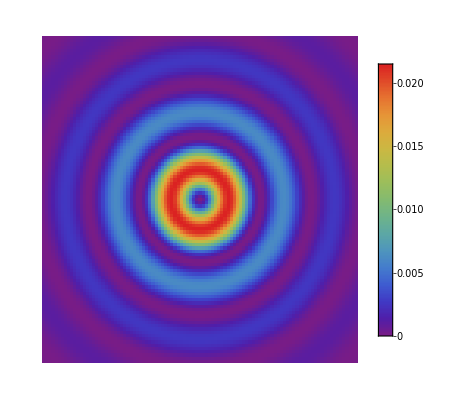

```mathematica
ArrayPlot[Abs[RHO2d[[All,All,3,1]]]^2,PlotLegends->Automatic,DataRange->{{min,max},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
```

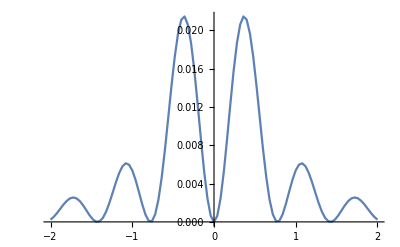

```mathematica
ListLinePlot[Abs[RHO1d[[3,1]]]^2,DataRange->{min,max},PlotRange->All]
```

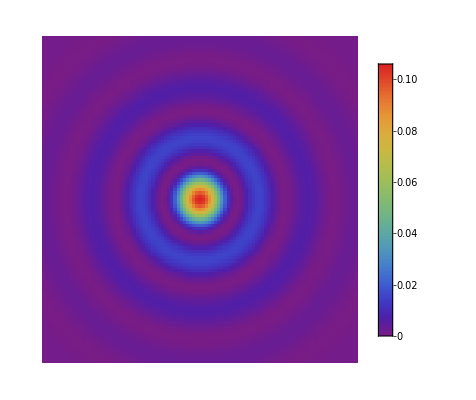

```mathematica
ArrayPlot[Abs[Z2d[[All,All,3,1]]]^2,PlotLegends->Automatic,DataRange->{{min,max},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
```

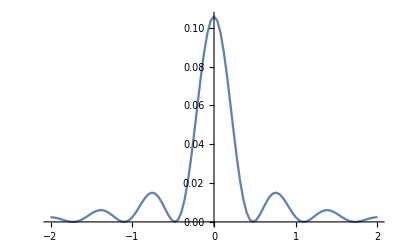

```mathematica
ListLinePlot[Abs[Z1d[[3,1]]]^2,DataRange->{min,max},PlotRange->All]
```

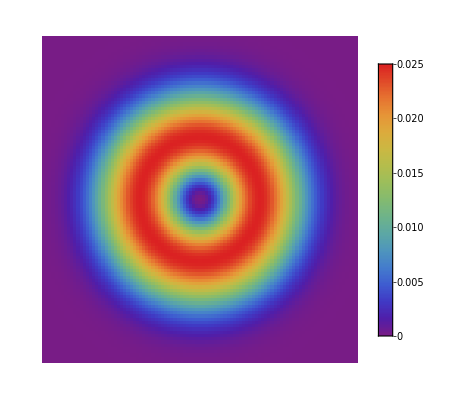

```mathematica
ArrayPlot[Abs[PHI2d[[All,All,3,1]]]^2,PlotLegends->Automatic,DataRange->{{min,max},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
```

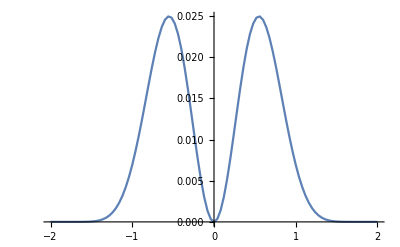

```mathematica
ListLinePlot[Abs[PHI1d[[3,1]]]^2,DataRange->{min,max},PlotRange->All]
```

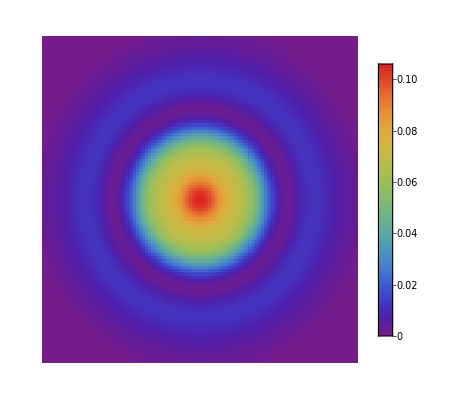

```mathematica
ArrayPlot[Abs[PHI2d[[All,All,3,1]]+RHO2d[[All,All,3,1]]+Z2d[[All,All,3,1]]]^2,PlotLegends->Automatic,DataRange->{{min,max},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
```

```mathematica
ListLinePlot[Abs[PHI1d[[3,1]]+Z1d[[3,1]]+RHO1d[[3,1]]]^2,DataRange->{min,max},PlotRange->All]
```